```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT]
```

```mathematica
leads=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/10sq/leads/lead_"<>ToString[x]<>".dat"]],{x,Range[-2.5,2.5,0.01]}]
```

{{{-0.497785-0.228643 ⅈ,0.130706+0.28624 ⅈ,0.0767826-0.159852 ⅈ,4,-0.0005428+0.0336017 ⅈ,0.0176555+0.0146533 ⅈ,-0.0134474-0.034101 ⅈ},8,{1}},500}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=(*Module[{J=Inverse[β[ω,δ,t,ϵ,m]],A:=Inverse[β[ω,δ,t,ϵ,m]],T:=T[t,m]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,180000];J=J]*)leads[[Round[ω*100+251]]]
```

```mathematica
IR[ω_]:= Inverse[IdentityMatrix[10]-LEFT[ω,0.0001,1,0,10].T[1,10].LEFT[ω,0.0001,1,0,10].T[1,10]].LEFT[ω,0.0001,1,0,10]
```

```mathematica
unit[ω_]:=β[ω,0.0001,1,0,10]
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
unit[ω_,δ_,t_,ϵ_,ϵ1_,n_]:=Module[{b=β[ω,0.0001,1,0,10]},ReplacePart[b,Table[F[RandomSample[{RandomInteger[{1,10}]},1]]//Flatten,n]->ω+ⅈ*δ-ϵ1]]
```

```mathematica
SL[ω_,ϵ1_]:=Module[{J= LEFT[ω,0.0001,1,0,10]},list={RandomSample[Join[Table[unit[ω,0.0001,1,0,ϵ1,1],10],Table[unit[ω,0.0001,1,0,0,1],10]]]};
Do[J=Inverse[IdentityMatrix[10]-Inverse[list[[1,a]]].T[1,10].J.T[1,10]].Inverse[list[[1,a]]],{a,20}];J=J]
```

```mathematica
GNONLR[ω_]:= LEFT[ω,0.0001,1,0,10].T[1,10].IR[ω]
```

```mathematica
GNONRL[ω_]:= IR[ω].T[1,10].LEFT[ω,0.0001,1,0,10]
```

```mathematica
γ[ω_]:= T[1,10].LEFT[ω,0.0001,1,0,10].T[1,10]
```

```mathematica
Σ[ω_]:= -2*Im[γ[ω]]
```

```mathematica
GNON[ω_,ϵ1_,num_]:=Module[{X= LEFT[ω,0.0001,1,0,10],list,recurs1,recurs},list={RandomSample[Join[Table[unit[ω,0.0001,1,0,ϵ1,1],num],Table[unit[ω,0.0001,1,0,0,1],100-num]]]};recurs1[m_]:=recurs1[m]=Module[{J= LEFT[ω,0.0001,1,0,10]},
Do[J=Inverse[IdentityMatrix[10]-Inverse[list[[1,a]]].T[1,10].J.T[1,10]].Inverse[list[[1,a]]],{a,m}];J=J];
recurs:=recurs=Table[recurs1[m],{m,100}];Inverse[IdentityMatrix[10]-X.T[1,10].recurs[[100]].T[1,10]].X.T[1,10].Module[{},Do[X=recurs[[m]].T[1,10].X,{m,100}];X=X]]
```

```mathematica
transmission[ω_,ϵ1_,num_]:= Abs[Tr[Σ[ω].GNON[ω,ϵ1,num].Σ[ω].ConjugateTranspose[GNON[ω,ϵ1,num]]]]
```

```mathematica
transmission[0,0.5,0]//AbsoluteTiming
```

{0.613722,9.82189}

```mathematica
Clear[GNON,transmission]
```

```mathematica
Mean[ParallelTable[transmission[0,0.5,10],500]]//AbsoluteTiming
```

{100.117,7.24553}

```mathematica
Mean[ParallelTable[transmission[0,0.5,10],500]]//AbsoluteTiming
```

{93.008,7.25045}

```mathematica
Mean[ParallelTable[transmission[0,0.5,20],500]]//AbsoluteTiming
```

{92.5978,5.45782}

```mathematica
Mean[ParallelTable[transmission[0,0.5,30],500]]//AbsoluteTiming
```

{93.317,4.16273}

```mathematica
Table[Mean[ParallelTable[transmission[1.5,0.5,num],500]],{num,10,90,10}]
```

{5.20438,4.59165,4.05742,3.62299,3.23279,2.89917,2.63781,2.36137,2.16513}

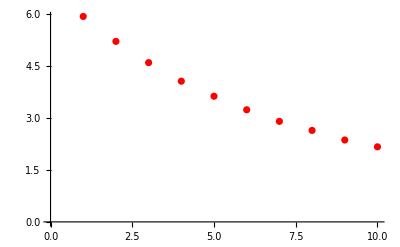

```mathematica
ListPlot[{5.92337,5.20438,4.591648748135393,4.057423757687342,3.6229941729878257,3.2327913864856557,2.899171610857492,2.6378090597725925,2.361367705750339,2.165134680364488},PlotStyle->Red]
```

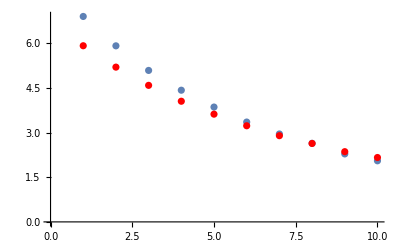

```mathematica
Show[%29,%34]
```

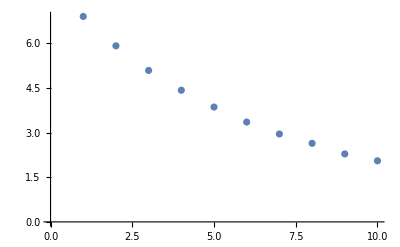

```mathematica
ListPlot[{6.90823,5.92052,5.093445018505563,4.42814398911832,3.8617608911123047,3.357631089907529,2.956135461972113,2.6417295363654025,2.2858776752941976,2.054476541179887}]
```

```mathematica
Mean[%98]
```

3.9709

```mathematica
transmission[1.5,0,10]
```

5.92337

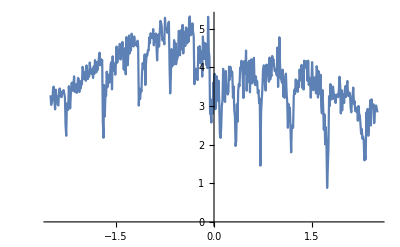

```mathematica
ListLinePlot[Table[{ω,transmission[ω,0.5,40]},{ω,Range[-2.5,2.5,0.01]}]]
```

```mathematica
{{0.,1.305201932147303*^-10},{0.02,0.00668733424897075},{0.04,0.0030320973550168936},{0.06,0.012036712180733827},{0.08,0.09417870588798655},{0.1,0.1479499076344234},{0.12,0.13131608832684089},{0.14,0.09808015052398324},{0.16,0.03398634553842027},{0.18,0.0663995871288719},{0.2,0.1674508953204324},{0.22,0.09012800884846847},{0.24,0.05348974332162882},{0.26,0.1461935728318367},{0.28,0.11921083035430752},{0.3,0.1317050196006171},{0.32,0.07597204728956321},{0.34,0.16396687517981012},{0.36,0.3471070064042149},{0.38,0.5342047818317531},{0.4,0.5380250098133528},{0.42,0.4056277905630058},{0.44,0.2927629489622681},{0.46,0.09414389073828372},{0.48,0.016487701585571213},{0.5,0.030244221943154716},{0.52,0.1418848574593175},{0.54,0.15636141523052577},{0.56,0.14306688338445528},{0.58,0.18571300479027023},{0.6,0.23352514753691764},{0.62,0.0799091129434393},{0.64,0.15433157531623842},{0.66,0.6189699238312053},{0.68,0.30069883982723106},{0.7000000000000001,0.24783229790246164},{0.72,0.4282097377533228},{0.74,0.4544478364899879},{0.76,0.35330510384046643},{0.78,0.060504820303280166},{0.8,0.049022250733539385},{0.8200000000000001,0.47180928372482683},{0.84,0.17545694324353275},{0.86,0.05452924848105707},{0.88,0.08677803033566431},{0.9,0.1779519214184951},{0.92,0.11564999235633167},{0.9400000000000001,0.13112974829464336},{0.96,0.5024381787942237},{0.98,0.3455232170139179},{1.,0.34964695314265454},{1.02,0.3194952833606049},{1.04,0.3450303177709893},{1.06,0.30615926699258933},{1.08,0.03077768108007553},{1.1,0.042244960047341254},{1.12,0.20936121526744203},{1.1400000000000001,0.09422528513034198},{1.16,0.07723166632276375},{1.18,0.08542824206462556},{1.2,0.16531384393228202},{1.22,0.24796338379294638},{1.24,0.13347936754496945},{1.26,0.26051500388373516},{1.28,0.22362516181682213},{1.3,0.7942402232164794},{1.32,0.36183470144715707},{1.34,0.1684588022581214},{1.36,0.10010963148512403},{1.3800000000000001,0.2520667337338976},{1.4000000000000001,0.0389534963347256},{1.42,0.23578351449149962},{1.44,0.02747576507025666},{1.46,0.11693646921731835},{1.48,0.2874127776624533},{1.5,0.13456531686322212},{1.52,0.7327383709272426},{1.54,0.1637789740780431},{1.56,0.049713794005591866},{1.58,0.28529104546688744},{1.6,0.42105241617182815},{1.62,0.14162240728583783},{1.6400000000000001,0.23719071664053998},{1.6600000000000001,0.18520394480728203},{1.68,0.28497027132400865},{1.7,0.014566326356088954},{1.72,0.1999139976663298},{1.74,0.015568562997460556},{1.76,0.05090127571802187},{1.78,0.10830595754961873},{1.8,0.15679615267491567},{1.82,0.27581824180395076},{1.84,0.29405694593255344},{1.86,0.05082583077760382},{1.8800000000000001,0.26595193967054515},{1.9000000000000001,0.6690711825892004},{1.92,0.19133419094494653},{1.94,0.22893068714418294},{1.96,0.4130317533886339},{1.98,0.19799221956084279},{2.,1.690341917946103*^-6},{2.02,1.2817192160896997*^-7},{2.04,5.669277743376236*^-7},{2.06,1.273834936476045*^-7},{2.08,2.314817530617885*^-7},{2.1,2.2694451676594267*^-9},{2.12,6.835206146856604*^-9},{2.14,2.8827237793388896*^-9},{2.16,8.117584353080554*^-8},{2.18,8.673995014441184*^-8},{2.2,4.6243021600882336*^-11},{2.22,4.78470634683303*^-11},{2.24,9.373562576236109*^-10},{2.2600000000000002,1.915213967716531*^-9},{2.2800000000000002,3.6715239456902894*^-11},{2.3000000000000003,9.05609035791077*^-11},{2.32,1.8701966257695176*^-8},{2.34,7.77716528158259*^-11},{2.36,1.3434621331463863*^-10},{2.38,4.5703561757179996*^-11},{2.4,7.893823687227839*^-10},{2.42,2.0494529207184774*^-10},{2.44,1.2774910906926456*^-10},{2.46,1.3649323506857113*^-9},{2.48,8.600182857188484*^-11},{2.5,7.413014232279976*^-12},{2.52,1.260988107028821*^-12},{2.54,1.3166770686756313*^-10},{2.56,2.3712183220542463*^-11},{2.58,7.665691966194457*^-12},{2.6,6.462078628978745*^-10},{2.62,1.3823428157312789*^-11},{2.64,2.099986050674848*^-10},{2.66,3.9181998126319673*^-10},{2.68,1.8987166199565676*^-10},{2.7,2.1040561420678524*^-13},{2.72,1.3976549749089518*^-13},{2.74,4.582080196938149*^-13},{2.7600000000000002,1.0146809155010384*^-10},{2.7800000000000002,4.432633669812684*^-11},{2.8000000000000003,2.7457720737471097*^-12},{2.82,1.4469146268006272*^-11},{2.84,9.497026519819302*^-13},{2.86,2.6221530121314056*^-12},{2.88,1.4540197668209387*^-10},{2.9,6.409540076211819*^-14},{2.92,1.8113146583140906*^-14},{2.94,6.729688586571942*^-12},{2.96,1.846755091868813*^-13},{2.98,8.285252651943612*^-14},{3.,4.327918604007199*^-12},{3.02,4.232703855503613*^-13},{3.04,1.4941651723120351*^-12},{3.06,2.8162867473756132*^-12},{3.08,9.652376869724665*^-12},{3.1,4.215478380928428*^-14},{3.12,1.5604733662609421*^-13},{3.14,1.3717324947073407*^-14},{3.16,3.1270121005248404*^-14},{3.18,1.8688481253808318*^-13},{3.2,6.297600342930739*^-14},{3.22,1.2016832689076155*^-14},{3.24,3.803188323482486*^-12},{3.2600000000000002,1.0025018133530567*^-13},{3.2800000000000002,1.783102557593353*^-13},{3.3000000000000003,5.800049477209817*^-13},{3.3200000000000003,8.224632076992815*^-16},{3.34,9.302279862826353*^-13},{3.36,1.201004022869439*^-12},{3.38,2.407973629576627*^-15},{3.4,1.1764561068843589*^-13},{3.42,4.42400912374593*^-14},{3.44,9.180402146717735*^-14},{3.46,6.716116941935922*^-15},{3.48,2.8541344123101375*^-16},{3.5,4.1365040373278846*^-14},{3.52,2.4717558648111177*^-14},{3.54,2.8559675703268146*^-15},{3.56,1.5792902038703469*^-15},{3.58,1.6070074619181042*^-13},{3.6,5.61848686712733*^-17},{3.62,5.299641599729293*^-15},{3.64,3.555971210133387*^-16},{3.66,3.173428601673886*^-16},{3.68,4.952813901875078*^-16},{3.7,5.305994188032278*^-15},{3.72,1.2171481216085491*^-15},{3.74,1.8941850104600946*^-17},{3.7600000000000002,1.3059760674121695*^-17},{3.7800000000000002,3.085406319056289*^-16},{3.8000000000000003,5.081276143002819*^-17},{3.8200000000000003,2.4262616880033932*^-15},{3.84,6.391799330944922*^-17},{3.86,4.569349079735391*^-16},{3.88,2.3581604057772123*^-18},{3.9,2.6339151775853067*^-16},{3.92,3.605008423661773*^-20},{3.94,4.503717324015694*^-20},{3.96,6.529858150063147*^-18},{3.98,3.451419238151877*^-20},{4.,7.867851284108802*^-22}}
```

{{0.,1.3052×10^-10},{0.02,0.00668733},{0.04,0.0030321},{0.06,0.0120367},{0.08,0.0941787},{0.1,0.14795},{0.12,0.131316},{0.14,0.0980802},{0.16,0.0339863},{0.18,0.0663996},{0.2,0.167451},{0.22,0.090128},{0.24,0.0534897},{0.26,0.146194},{0.28,0.119211},{0.3,0.131705},{0.32,0.075972},{0.34,0.163967},{0.36,0.347107},{0.38,0.534205},{0.4,0.538025},{0.42,0.405628},{0.44,0.292763},{0.46,0.0941439},{0.48,0.0164877},{0.5,0.0302442},{0.52,0.141885},{0.54,0.156361},{0.56,0.143067},{0.58,0.185713},{0.6,0.233525},{0.62,0.0799091},{0.64,0.154332},{0.66,0.61897},{0.68,0.300699},{0.7,0.247832},{0.72,0.42821},{0.74,0.454448},{0.76,0.353305},{0.78,0.0605048},{0.8,0.0490223},{0.82,0.471809},{0.84,0.175457},{0.86,0.0545292},{0.88,0.086778},{0.9,0.177952},{0.92,0.11565},{0.94,0.13113},{0.96,0.502438},{0.98,0.345523},{1.,0.349647},{1.02,0.319495},{1.04,0.34503},{1.06,0.306159},{1.08,0.0307777},{1.1,0.042245},{1.12,0.209361},{1.14,0.0942253},{1.16,0.0772317},{1.18,0.0854282},{1.2,0.165314},{1.22,0.247963},{1.24,0.133479},{1.26,0.260515},{1.28,0.223625},{1.3,0.79424},{1.32,0.361835},{1.34,0.168459},{1.36,0.10011},{1.38,0.252067},{1.4,0.0389535},{1.42,0.235784},{1.44,0.0274758},{1.46,0.116936},{1.48,0.287413},{1.5,0.134565},{1.52,0.732738},{1.54,0.163779},{1.56,0.0497138},{1.58,0.285291},{1.6,0.421052},{1.62,0.141622},{1.64,0.237191},{1.66,0.185204},{1.68,0.28497},{1.7,0.0145663},{1.72,0.199914},{1.74,0.0155686},{1.76,0.0509013},{1.78,0.108306},{1.8,0.156796},{1.82,0.275818},{1.84,0.294057},{1.86,0.0508258},{1.88,0.265952},{1.9,0.669071},{1.92,0.191334},{1.94,0.228931},{1.96,0.413032},{1.98,0.197992},{2.,1.69034×10^-6},{2.02,1.28172×10^-7},{2.04,5.66928×10^-7},{2.06,1.27383×10^-7},{2.08,2.31482×10^-7},{2.1,2.26945×10^-9},{2.12,6.83521×10^-9},{2.14,2.88272×10^-9},{2.16,8.11758×10^-8},{2.18,8.674×10^-8},{2.2,4.6243×10^-11},{2.22,4.78471×10^-11},{2.24,9.37356×10^-10},{2.26,1.91521×10^-9},{2.28,3.67152×10^-11},{2.3,9.05609×10^-11},{2.32,1.8702×10^-8},{2.34,7.77717×10^-11},{2.36,1.34346×10^-10},{2.38,4.57036×10^-11},{2.4,7.89382×10^-10},{2.42,2.04945×10^-10},{2.44,1.27749×10^-10},{2.46,1.36493×10^-9},{2.48,8.60018×10^-11},{2.5,7.41301×10^-12},{2.52,1.26099×10^-12},{2.54,1.31668×10^-10},{2.56,2.37122×10^-11},{2.58,7.66569×10^-12},{2.6,6.46208×10^-10},{2.62,1.38234×10^-11},{2.64,2.09999×10^-10},{2.66,3.9182×10^-10},{2.68,1.89872×10^-10},{2.7,2.10406×10^-13},{2.72,1.39765×10^-13},{2.74,4.58208×10^-13},{2.76,1.01468×10^-10},{2.78,4.43263×10^-11},{2.8,2.74577×10^-12},{2.82,1.44691×10^-11},{2.84,9.49703×10^-13},{2.86,2.62215×10^-12},{2.88,1.45402×10^-10},{2.9,6.40954×10^-14},{2.92,1.81131×10^-14},{2.94,6.72969×10^-12},{2.96,1.84676×10^-13},{2.98,8.28525×10^-14},{3.,4.32792×10^-12},{3.02,4.2327×10^-13},{3.04,1.49417×10^-12},{3.06,2.81629×10^-12},{3.08,9.65238×10^-12},{3.1,4.21548×10^-14},{3.12,1.56047×10^-13},{3.14,1.37173×10^-14},{3.16,3.12701×10^-14},{3.18,1.86885×10^-13},{3.2,6.2976×10^-14},{3.22,1.20168×10^-14},{3.24,3.80319×10^-12},{3.26,1.0025×10^-13},{3.28,1.7831×10^-13},{3.3,5.80005×10^-13},{3.32,8.22463×10^-16},{3.34,9.30228×10^-13},{3.36,1.201×10^-12},{3.38,2.40797×10^-15},{3.4,1.17646×10^-13},{3.42,4.42401×10^-14},{3.44,9.1804×10^-14},{3.46,6.71612×10^-15},{3.48,2.85413×10^-16},{3.5,4.1365×10^-14},{3.52,2.47176×10^-14},{3.54,2.85597×10^-15},{3.56,1.57929×10^-15},{3.58,1.60701×10^-13},{3.6,5.61849×10^-17},{3.62,5.29964×10^-15},{3.64,3.55597×10^-16},{3.66,3.17343×10^-16},{3.68,4.95281×10^-16},{3.7,5.30599×10^-15},{3.72,1.21715×10^-15},{3.74,1.89419×10^-17},{3.76,1.30598×10^-17},{3.78,3.08541×10^-16},{3.8,5.08128×10^-17},{3.82,2.42626×10^-15},{3.84,6.3918×10^-17},{3.86,4.56935×10^-16},{3.88,2.35816×10^-18},{3.9,2.63392×10^-16},{3.92,3.60501×10^-20},{3.94,4.50372×10^-20},{3.96,6.52986×10^-18},{3.98,3.45142×10^-20},{4.,7.86785×10^-22}}

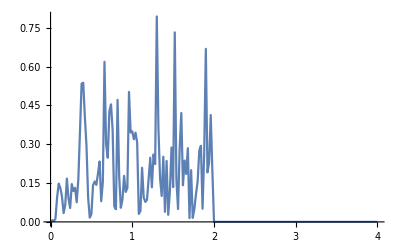

```mathematica
ListPlot[%19,Joined->True]
```